### Fourier Transform

```mathematica
ϕb[x_,t_]=-ϕ[x,t]+ϕ[x,t]^3-ϵ^2*D[ϕ[x,t],{x,2}];
eq1=D[ϕ[x,t], t] == Dϕ*D[Subscript[A, b]*(2*ϕb[x,t]*(-1+3*ϕ[x,t]^2-2*ϵ*β*u[x,t]^2*ϕ[x,t])-2*ϵ^2*D[ϕb[x,t],{x,2}])+4 Subscript[A, s]*ϕ[x,t]*(ϕ[x,t]^2-1)*u[x,t]^2*(u[x,t]-umax)^2+ 2 Subscript[A, f]*ϕ[x,t]*u[x,t]^2-2*σ*(u[x,t]^2*D[ϕ[x,t], {x,2}]+2*u[x,t]*D[u[x,t],x]*D[ϕ[x,t],x]),{x,2}];

eq2=D[u[x,t],t]== Du*D[Subscript[A, b]*4*ϵ*β*u[x,t]*(1-ϕ[x,t]^2)*ϕb[x,t]+2*Subscript[A, s]*((u[x,t]*(u[x,t]-umax)*(2*u[x,t]-umax))*(ϕ[x,t]^2-1)^2-λ*D[u[x,t],{x,2}])+2*Subscript[A, f] ϕ[x,t]^2*u[x,t],{x,2}]+Subscript[λ, 1]*D[D[ϕ[x,t],{x,2}]*u[x,t]+2*σ*u[x,t]*D[ϕ[x,t],x]^2,{x,2}];


rules={ϕ->Function[{x,t},Subscript[ϕ, 0]+δ*Subscript[ϕ, 1][x,t]],u->Function[{x,t},Subscript[u, 0]+δ*Subscript[u, 1][x,t]]};

rhs1=eq1[[2]]/.rules//Expand;
rhs2=eq2[[2]]/.rules//Expand;

lin1=Coefficient[rhs1,δ,1];
lin2=Coefficient[rhs2,δ,1]

fourierRules={D[Subscript[ϕ, 1][x,t],{x,2}]->-k^2 Subscript[ϕ, 1][x,t],D[Subscript[u, 1][x,t],{x,2}]->-k^2 Subscript[u, 1][x,t],D[Subscript[ϕ, 1][x,t],{x,4}]->k^4 Subscript[ϕ, 1][x,t],D[Subscript[u, 1][x,t],{x,4}]->k^4 Subscript[u, 1][x,t]};
lin1k=lin1/.fourierRules//Simplify
lin2k=lin2/.fourierRules//Simplify

vars={Subscript[ϕ, 1][x,t],Subscript[u, 1][x,t]};
J=Outer[D,{lin1k,lin2k},vars]//Simplify;
Eigenvalues[J];
```

2 Du umax^2 A_s u_1^(2,0)[x,t]-12 Du umax A_s u_0 u_1^(2,0)[x,t]+12 Du A_s u_0^2 u_1^(2,0)[x,t]-4 Du β ϵ A_b ϕ_0 u_1^(2,0)[x,t]+2 Du A_f ϕ_0^2 u_1^(2,0)[x,t]-4 Du umax^2 A_s ϕ_0^2 u_1^(2,0)[x,t]+24 Du umax A_s u_0 ϕ_0^2 u_1^(2,0)[x,t]-24 Du A_s u_0^2 ϕ_0^2 u_1^(2,0)[x,t]+8 Du β ϵ A_b ϕ_0^3 u_1^(2,0)[x,t]+2 Du umax^2 A_s ϕ_0^4 u_1^(2,0)[x,t]-12 Du umax A_s u_0 ϕ_0^4 u_1^(2,0)[x,t]+12 Du A_s u_0^2 ϕ_0^4 u_1^(2,0)[x,t]-4 Du β ϵ A_b ϕ_0^5 u_1^(2,0)[x,t]-4 Du β ϵ A_b u_0 ϕ_1^(2,0)[x,t]+4 Du A_f u_0 ϕ_0 ϕ_1^(2,0)[x,t]-8 Du umax^2 A_s u_0 ϕ_0 ϕ_1^(2,0)[x,t]+24 Du umax A_s u_0^2 ϕ_0 ϕ_1^(2,0)[x,t]-16 Du A_s u_0^3 ϕ_0 ϕ_1^(2,0)[x,t]+24 Du β ϵ A_b u_0 ϕ_0^2 ϕ_1^(2,0)[x,t]+8 Du umax^2 A_s u_0 ϕ_0^3 ϕ_1^(2,0)[x,t]-24 Du umax A_s u_0^2 ϕ_0^3 ϕ_1^(2,0)[x,t]+16 Du A_s u_0^3 ϕ_0^3 ϕ_1^(2,0)[x,t]-20 Du β ϵ A_b u_0 ϕ_0^4 ϕ_1^(2,0)[x,t]-2 Du λ A_s u_1^(4,0)[x,t]-4 Du β ϵ^3 A_b u_0 ϕ_1^(4,0)[x,t]+u_0 λ_1 ϕ_1^(4,0)[x,t]+4 Du β ϵ^3 A_b u_0 ϕ_0^2 ϕ_1^(4,0)[x,t]

2 Dϕ (-4 k^2 β ϵ A_b u_0 ϕ_0^2 u_1[x,t]+4 k^2 β ϵ A_b u_0 ϕ_0^4 u_1[x,t]-k^2 A_b ϕ_1[x,t]+2 k^4 ϵ^2 A_b ϕ_1[x,t]-k^4 σ u_0^2 ϕ_1[x,t]-4 k^2 β ϵ A_b u_0^2 ϕ_0 ϕ_1[x,t]+2 k^4 β ϵ^3 A_b u_0^2 ϕ_0 ϕ_1[x,t]+12 k^2 A_b ϕ_0^2 ϕ_1[x,t]-6 k^4 ϵ^2 A_b ϕ_0^2 ϕ_1[x,t]+8 k^2 β ϵ A_b u_0^2 ϕ_0^3 ϕ_1[x,t]-15 k^2 A_b ϕ_0^4 ϕ_1[x,t]-k^2 A_f u_0 (2 ϕ_0 u_1[x,t]+u_0 ϕ_1[x,t])-2 k^2 A_s (umax-u_0) u_0 (-2 (umax-2 u_0) ϕ_0 u_1[x,t]+2 (umax-2 u_0) ϕ_0^3 u_1[x,t]+u_0 (-umax+u_0) ϕ_1[x,t]+3 (umax-u_0) u_0 ϕ_0^2 ϕ_1[x,t])+ϵ^4 A_b ϕ_1^(6,0)[x,t])

k^2 (-2 Du A_f ϕ_0^2 u_1[x,t]+k^2 u_0 λ_1 ϕ_1[x,t]-4 Du A_f u_0 ϕ_0 ϕ_1[x,t]+4 Du β ϵ A_b (-1+ϕ_0^2) (-ϕ_0 u_1[x,t]+ϕ_0^3 u_1[x,t]+(-1+k^2 ϵ^2) u_0 ϕ_1[x,t]+5 u_0 ϕ_0^2 ϕ_1[x,t])-2 Du A_s ((umax^2+k^2 λ-2 umax^2 ϕ_0^2+umax^2 ϕ_0^4-6 umax u_0 (-1+ϕ_0^2)^2+6 u_0^2 (-1+ϕ_0^2)^2) u_1[x,t]+4 u_0 (umax^2-3 umax u_0+2 u_0^2) ϕ_0 (-1+ϕ_0^2) ϕ_1[x,t]))

### Plot

{{0.1 k^2 (-1.12+0.04 k^2-0.0032 ϕ_0+0.000064 k^2 ϕ_0+12. ϕ_0^2-0.24 k^2 ϕ_0^2+0.0064 ϕ_0^3-15. ϕ_0^4-1.296 (-1+3 ϕ_0^2)),0.04 k^2 ϕ_0 (-3-2 (14.4-0.02 ϕ_0) (-1+ϕ_0^2))},{0.2 k^2 (0.1 k^2-1.2 ϕ_0-11.52 ϕ_0 (-1+ϕ_0^2)+0.008 (-1+ϕ_0^2) (-1+0.04 k^2+5 ϕ_0^2)),k^2 (-1. (4+0.6 k^2-8 ϕ_0^2+4 ϕ_0^4-2.16 (-1+ϕ_0^2)^2)+0.2 ϕ_0 (-3 ϕ_0+0.04 (-1+ϕ_0^2)^2))}}

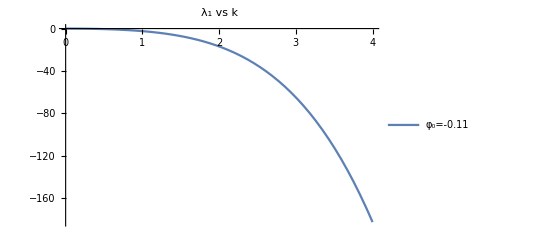

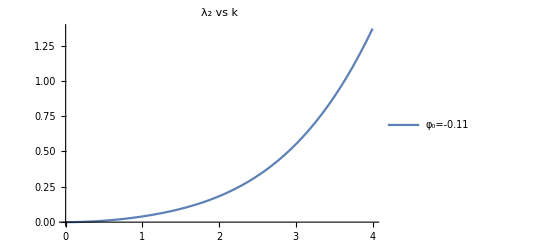

```mathematica
params={Subscript[A, s]->5,Subscript[A, f]->3,umax->2,σ->1,λ->0.6,Subscript[λ, 1]->0.1,Du->0.1,Dϕ->0.05,Subscript[u, 0]->0.2,ϵ-> 0.2, β-> 0.1, Subscript[A, b]->1.0};
Jnum=J/.params

eig[k_?NumericQ,phi_?NumericQ]:=Eigenvalues[N[Jnum/.Subscript[ϕ, 0]->phi]];
eig1[k_?NumericQ,phi_?NumericQ]:=eig[k,phi][[1]];
eig2[k_?NumericQ,phi_?NumericQ]:=eig[k,phi][[2]];
phiVals={-0.11};

Plot[Evaluate@Table[Re[eig1[k,phiVals[[i]]]],{i,Length[phiVals]}],{k,0,4},PlotLegends->Table["φ_0="<>ToString[phiVals[[i]]],{i,Length[phiVals]}],PlotLabel->"λ_1 vs k"]

Plot[Evaluate@Table[Re[eig2[k,phiVals[[i]]]],{i,Length[phiVals]}],{k,0,4},PlotLegends->Table["φ_0="<>ToString[phiVals[[i]]],{i,Length[phiVals]}],PlotLabel->"λ_2 vs k"]
```

```mathematica
params={k->7,Subscript[ϕ, 0]->0};
Jnum2=Jnum/.params
```

{{-226.38,0.},{0.,-258.72}}

```mathematica
params={k->1,Subscript[ϕ, 0]->0};
Jnum2=Jnum/.params
```

{{0.2696,0.},{0.,1.4}}

```mathematica
params={Subscript[A, s]->2,Subscript[A, f]->2,umax->3,σ->1,λ->1.0,Subscript[λ, 1]->0.,Du->0.1,Dϕ->0.01,Subscript[u, 0]->1.5,ϵ-> 0.01, β->0.2, Subscript[A, b]->0.02};

Jnum=J/.params

eig[k_,phi_]:=SortBy[Eigenvalues[N[Jnum/.{Subscript[ϕ, 0]->phi,k->k}]],Re];

kVals=Range[0,4,0.01];
phiVals={-0.};

data=Flatten[Table[With[{ev=eig[k,phi]},{k,phi,Re[ev[[1]]],Re[ev[[2]]]}],{phi,phiVals},{k,kVals}],1];

Export["/home/soumyadeep/Desktop/Active_Gel/My_Codes/02a_eigen_data.csv",N[data]]
```

{{-0.02 k^2 (4.5+2.25 k^2+20.25 (-1+3 ϕ_0^2)+0.02 (1-12 ϕ_0^2+15 ϕ_0^4)),-0.12 k^2 ϕ_0},{-1.5 k^2 (0.+0.8 ϕ_0),-0.2 k^2 (2 ϕ_0^2+2 (9+1. k^2-18 ϕ_0^2+9 ϕ_0^4-13.5 (-1+ϕ_0^2)^2))}}

/home/soumyadeep/Desktop/Active_Gel/My_Codes/02a_eigen_data.csv